```mathematica
NotebookEvaluate[
"~/Documents/Sparse\ Grids/Checking\ SBP/Methods\ and\ Functions\ for\ SBP.nb"]
```

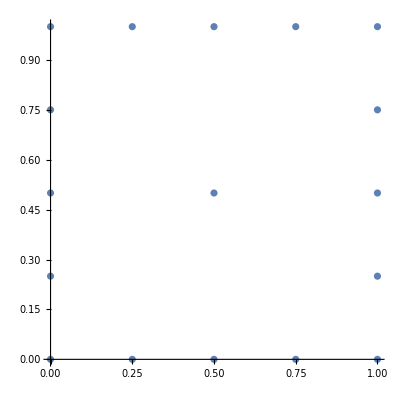

```mathematica
ListPlot[Flatten[makeSparse[2],3],AspectRatio->1]
```

### Finding the weights and then integrating

```mathematica
(*Worth noting: it isn't necessary to find the weights if we just integrate in our sparse coefficient space. This is equivalent and computationally lighter. *)
```

```mathematica
Table[switch3[kx,i]switch3[ky,j]/.kx->3/.ky->3,{i,0,8},{j,0,8}]//MatrixForm
```

(1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64)

```mathematica
showFullWeights[lx_,ly_]:=Sum[Table[weights1D[i,kx,lx] weights1D[j,ky,ly],{i,0,2^lx},{j,0,2^ly}],{kx,0,lx},{ky,0,ly}]

showWeights[n_]:=Sum[Sum[Table[weights1D[i,getrow[perp,diag],n]weights1D[j,getcol[perp,diag],n],{i,0,2^n},{j,0,2^n}],{perp,0,endperp[diag]-1}],{diag,0,n}]

showWeights[n_,i_,j_]:=Sum[Sum[weights1D[i,getrow[perp,diag],n]weights1D[j,getcol[perp,diag],n],{perp,0,endperp[diag]-1}],{diag,0,n}]
```

```mathematica
computeSum[n_]:=Sum[posW[i/2^n]posW[j/2^n]#[[i+1,j+1]],{i,0,2^n},{j,0,2^n}]&@showWeights[n]
```

```mathematica
Table[computeSum[n],{n,0,6}]
```

{1,1,1,1,1,1,1}

```mathematica
weights1D[i_,kx_,lx_]:=If[Mod[i,2^(lx-kx)]==0,switch3[kx,2^(kx-lx)i],0]
```

```mathematica
showFullWeights[1,1]
```

{{1/4,1/4,1/4},{1/4,1/4,1/4},{1/4,1/4,1/4}}

```mathematica
computeSum2[n_]:=Sum[Sum[Sum[posW[switch2[getrow[perp,diag]] i]posW[switch2[getcol[perp,diag]] j] Sum[],{i,1,2^switch[getrow[perp,diag]],2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]
```

```mathematica
SparsetoPosition[coefficients_,n_]:=standardCoefficients2D[sparseReconstruct[reverseFlattenSparse[coefficients,n]],n,n]
```

```mathematica
SparsetoPosition[dxMatrixSparse[3][[4]],3]
```

{{0,0,0,0,0,0,0,0,0},{-11,-11,-11,-11,-11,-11,-11,-11,-11},{-6,-6,-6,-6,-6,-6,-6,-6,-6},{-5,-5,-5,-5,-5,-5,-5,-5,-5},{-4,-4,-4,-4,-4,-4,-4,-4,-4},{-5,-5,-5,-5,-5,-5,-5,-5,-5},{-6,-6,-6,-6,-6,-6,-6,-6,-6},{-11,-11,-11,-11,-11,-11,-11,-11,-11},{0,0,0,0,0,0,0,0,0}}

```mathematica
sparseCoefficients2D[Sin[#1+#2]&,3]
sparseCoefficients2D[Sin[#1+#2]&,3]//Flatten
reverseFlattenSparse[sparseCoefficients2D[Sin[#1+#2]&,3]//Flatten,3]
```

{{{{0}}},{{{Sin[1]}},{{-2 Sin[1]+Sin[2]}},{{Sin[1]}}},{{{0.05869}},{{0.0634207}},{{0.0634207}},{{0.05869}}},{{{0.00769119,0.0211905}},{{0.0218104,0.00939924}},{{0.0126103}},{{0.0218104},{0.00939924}},{{0.00769119},{0.0211905}}},{{{0.000972754,0.00285778,0.00456512,0.00598863}},{{0.00606704,0.00479547,0.00322575,0.00145546}},{{0.00259409,0.00361151}},{{0.00259409},{0.00361151}},{{0.00606704},{0.00479547},{0.00322575},{0.00145546}},{{0.000972754},{0.00285778},{0.00456512},{0.00598863}}}}

{0,Sin[1],-2 Sin[1]+Sin[2],Sin[1],0.05869,0.0634207,0.0634207,0.05869,0.00769119,0.0211905,0.0218104,0.00939924,0.0126103,0.0218104,0.00939924,0.00769119,0.0211905,0.000972754,0.00285778,0.00456512,0.00598863,0.00606704,0.00479547,0.00322575,0.00145546,0.00259409,0.00361151,0.00259409,0.00361151,0.00606704,0.00479547,0.00322575,0.00145546,0.000972754,0.00285778,0.00456512,0.00598863}

{{{{0}}},{{{Sin[1]}},{{-2 Sin[1]+Sin[2]}},{{Sin[1]}}},{{{0.05869}},{{0.0634207}},{{0.0634207}},{{0.05869}}},{{{0.00769119,0.0211905}},{{0.0218104,0.00939924}},{{0.0126103}},{{0.0218104},{0.00939924}},{{0.00769119},{0.0211905}}},{{{0.000972754,0.00285778,0.00456512,0.00598863}},{{0.00606704,0.00479547,0.00322575,0.00145546}},{{0.00259409,0.00361151}},{{0.00259409},{0.00361151}},{{0.00606704},{0.00479547},{0.00322575},{0.00145546}},{{0.000972754},{0.00285778},{0.00456512},{0.00598863}}}}

### Integrating By Coefficients

```mathematica
sparseIntegrateByCoefficients[f_,n_]:=Sum[Sum[Sum[#[[diag+2,perp+2,i,j]] area[getrow[perp,diag]] area[getcol[perp,diag]],{i,1,2^(switch[getrow[perp,diag]]-1)},{j,1,2^(switch[getcol[perp,diag]]-1)}]
,{perp,-1,endperp[diag]}],{diag,-1,n}]&@sparseCoefficients2D[f,n]
```

```mathematica
sparseIntegrateByCoefficients[Cos[#1+#2]&,10]//N
NIntegrate[Cos[x+y],{x,0,1},{y,0,1}]
```

0.496751

0.496751

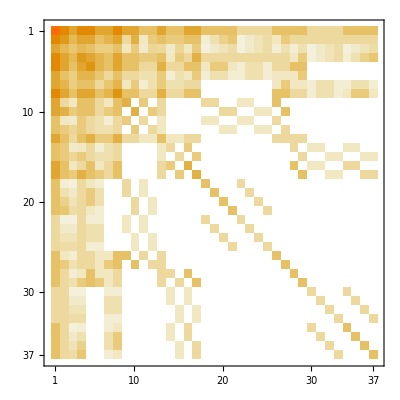

```mathematica
Out[283]//MatrixPlot
```

```mathematica
W3=sparseW[3];
dW3=sparsedW[3];
D3=dxMatrixSparse[3];
Δ3=(#+Transpose[#]-dW3)&@(W3.D3);
```

```mathematica
SparsetoPosition[dxMatrixSparse]
```

standardProject2D[∑_(diag=-1)^(Length[dxMatrixSparse]-2) (∑_(perp=-1)^endperp[diag] dxMatrixSparse⟦diag+2,perp+2,ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]⟧ ϕ[getrow[perp,diag],getcol[perp,diag],ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]][#1,#2])&]

```mathematica
Chop[Eigenvalues[W3]]
```

{2.83586,0.45264,0.450277,0.38209,0.337294,0.329702,0.174701,0.174065,0.173464,0.161541,0.156176,0.155433,-0.147342,0.0995419,0.0992044,-0.0723677,0.0441749,-0.0405828,0.0360383,-0.030854,-0.0307339,0.0270183,0.0269607,0.0249135,0.0238997,-0.0119262,-0.0117895,-0.00689938,0,0,0,0,0,0,0,0,0}

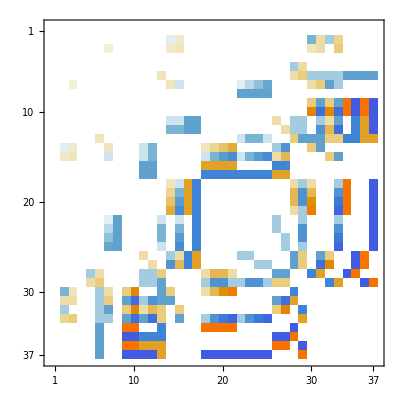

```mathematica
Δ3//MatrixPlot
```

```mathematica
(#+Transpose[#]-dW3)&@(W3.D3-1/2 Δ3)
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
sparseBasis[n_]:=Flatten[Table[sparseCoefficients2D[ψ[n,n,i,j],n]//Flatten,{i,0,2^n},{j,0,2^n}],1]//Transpose
```

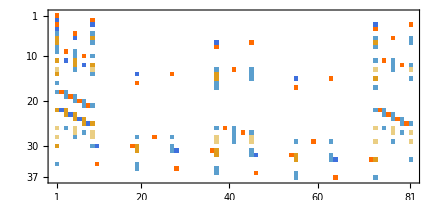

```mathematica
sparseBasis[3]//MatrixPlot
```

```mathematica
sparseWeights[n_]:=Table[sparseIntegrateByCoefficients[ψ[n,n,i,j],n],{i,0,2^n},{j,0,2^n}]
fullWeights[kx_,ky_]:=Table[fullIntegrate[ψ[kx,ky,i,j],kx,ky],{i,0,2^kx},{j,0,2^ky}]
```

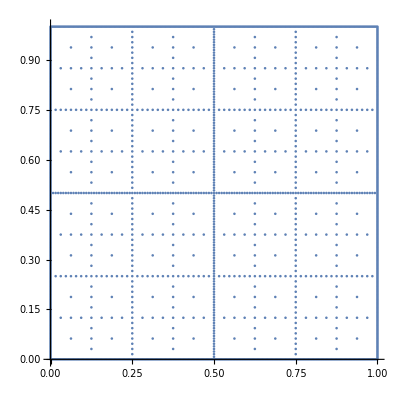

```mathematica
ListPlot[Flatten[makeSparse[8],3],AspectRatio->1]
```

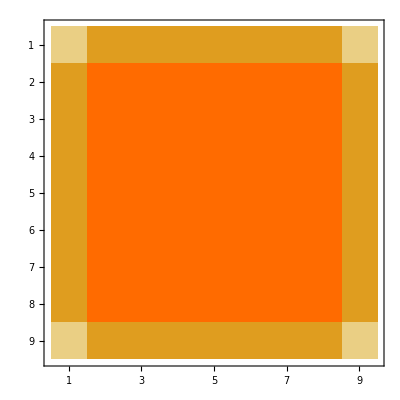

```mathematica
fullWeights[3,3]//MatrixPlot
```

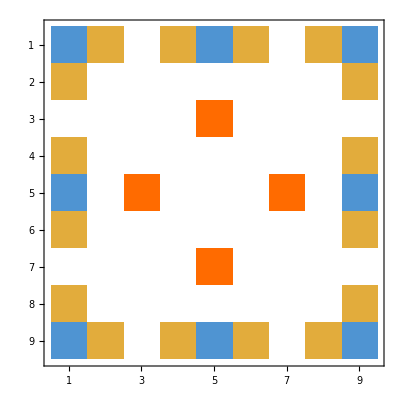

```mathematica
sparseWeights[3]//MatrixPlot
```

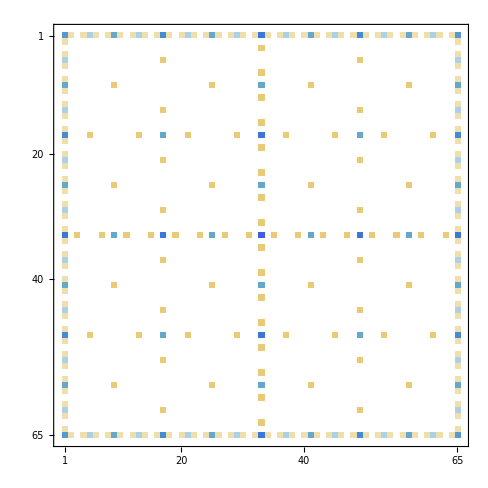

```mathematica
sparseWeights[6]//MatrixPlot
```

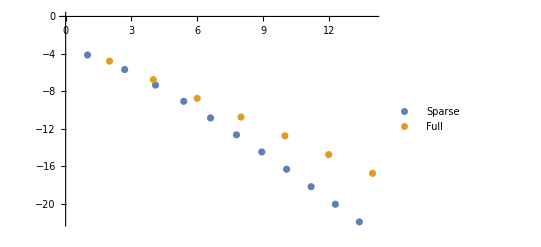

```mathematica
ListPlot[{Table[{n+Log[n],Log2[Abs[sparseIntegrateByCoefficients[Sin[#1+#2]^2 Cos[#2]&,n]-NIntegrate[Sin[x+y]^2 Cos[y],{x,0,1},{y,0,1}]]]},{n,1,11}],
Table[{2n,Log2[Abs[fullIntegrate[Sin[#1+#2]^2 Cos[#2]&,n,n]-NIntegrate[Sin[x+y]^2 Cos[y],{x,0,1},{y,0,1}]]]},{n,1,7}]},PlotLegends->{"Sparse","Full"}]
```

The integration for the sparse grid is working just as we want.

```mathematica
sparseWeights[5]//MatrixForm
```

(-0.03125 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.03125 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.046875 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.03125 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.03125
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.015625
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.03125 | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | -0.03125 | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | -0.03125
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.015625
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.046875 | 0. | 0.03125 | 0. | 0. | 0. | 0.03125 | 0. | -0.03125 | 0. | 0.03125 | 0. | 0. | 0. | 0.03125 | 0. | -0.0625 | 0. | 0.03125 | 0. | 0. | 0. | 0.03125 | 0. | -0.03125 | 0. | 0.03125 | 0. | 0. | 0. | 0.03125 | 0. | -0.046875
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.015625
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.03125 | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | -0.03125 | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | -0.03125
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.015625
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.015625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.015625
-0.03125 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.03125 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.046875 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.03125 | 0.015625 | 0. | 0.015625 | -0.015625 | 0.015625 | 0. | 0.015625 | -0.03125)